# A Quick Review of the Wolfram Quantum Computation Framework

## Paclet Installation

Deployed version:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
```

PacletObject[…]

Development version:

```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall->True]
```

PacletObject[…]

Get the paclet:

```mathematica
<<Wolfram`QuantumFramework`
```

QuantumBasis::shdw: Symbol QuantumBasis appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

LibraryFunction::noopen: Cannot open libcotengra.

## QuantumCircuitOperator

A quantum circuit is a composition of quantum operators acting on a quantum state, representing a stepwise transformation of a quantum system.

QuantumCircuitOperator[{op1,op1,op2}] a list of operators (either complete form, or shorthand)

QuantumCircuitOperator[{"named_circuit",...}] a named circuit

QuantumCircuitOperator[...][ ] a circuit acting on its corresponding register state 

QuantumCircuitOperator[...][ "Diagram"] shows the diagram 
QuantumCircuitOperator[...][ "CircuitOperator"] shows the summary properties ..[“TensorNetwork”]
ctrl shift T - traditional form - shows bra-kets 
ctrl shift N - normal form
use
//FullSimplify

```mathematica
QuantumCircuitOperator["X"]
```

QuantumCircuitOperator[…]

```mathematica
QuantumCircuitOperator["XYZ"]
```

QuantumCircuitOperator[…]

```mathematica
QuantumCircuitOperator[{"X"->2}]
```

QuantumCircuitOperator[…]

```mathematica
QuantumCircuitOperator[{"X"->2,"H","Z"->2}]
```

QuantumCircuitOperator[…]

```mathematica
QuantumCircuitOperator[{"CNOT"}]
```

QuantumCircuitOperator[…]

```mathematica
QuantumCircuitOperator[{"CNOT"->{2,1}}]
```

QuantumCircuitOperator[…]

```mathematica
QuantumCircuitOperator[{"X"->2,"H","Z"->2}]["Operators"]
```

{QuantumOperator[…],QuantumOperator[…],QuantumOperator[…]}

```mathematica
QuantumCircuitOperator[{"X"->2,"H","Z"->2}]["CircuitOperator"]
```

QuantumOperator[…]

```mathematica
QuantumCircuitOperator[{"H","CNOT",Sqrt@"X","Barrier","RootSWAP",{"R",θ,"X"->1,"Y"->2},{"Permutation",Cycles[{{1,2}}]},"Barrier",QuantumChannel[{"BitFlip",p}],"Barrier",{1},{2}}]
```

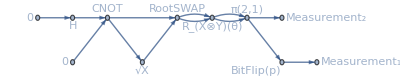

```mathematica
QuantumCircuitOperator[…]["TensorNetwork"]
```

```mathematica
%["Operators"]
```

```mathematica
QuantumCircuitOperator[{"X"->1,"Y"->2,QuantumOperator[{"R",θ,"X"->1,"Y"->2}]}][]["Formula"]//FullSimplify
```

ⅈ (-1/2 ⅈ ⅇ^(-(ⅈ θ)/2)+1/2 ⅈ ⅇ^((ⅈ θ)/2))00+ⅈ (1/2 ⅇ^(-(ⅈ θ)/2)+1/2 ⅇ^((ⅈ θ)/2))11

## QuantumOperators

The most important pattern to remember is QuantumOperator[arg,order]:

```mathematica
QuantumOperator["X"]
```

QuantumOperator[…]

```mathematica
QuantumOperator[("X",3),{2}]
```

```mathematica
QuantumOperator[…]
```

By default, the order is set as {1}, {1,2} or {1,2,...} (depending on the operator):

```mathematica
QuantumOperator["SWAP"]

QuantumOperator["SWAP"]
```

QuantumOperator[…]

QuantumOperator[…]

QuantumOperator[…]

```mathematica
QuantumOperator[{"Permutation",Cycles[{{1,2}}]}]
```

```mathematica
QuantumOperator[…]
```

```mathematica
QuantumOperator[{"Permutation",Cycles[{{1,2}}]}]
```

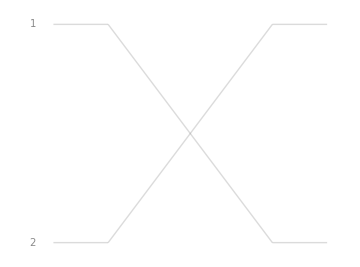

```mathematica
QuantumCircuitOperator[QuantumOperator[{"Permutation",Cycles[{{1,2}}]}]]["Diagram"]
```

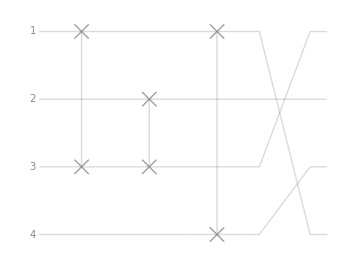

```mathematica
QuantumCircuitOperator[{"SWAP"->{1,3},"SWAP"->{2,3},"SWAP"->{1,4},QuantumOperator[{"Permutation",Cycles[{{3,1,4}}]}]}]["Diagram"]
```

```mathematica
QuantumOperator["SWAP"]==QuantumOperator[{"Permutation",Cycles[{{1,2}}]}]
```

True

```mathematica
QuantumOperator["SWAP",{2,3}]
```

QuantumOperator[…]

```mathematica
QuantumOperator["SWAP",{2,3}]
```

```mathematica
QuantumOperator["X",{1,2}]==QuantumOperator["X"]@QuantumOperator["X",{2}]==QuantumTensorProduct[QuantumOperator["X"],QuantumOperator["X"]]
```

True

```mathematica
QuantumOperator["X",{1,2}]==QuantumOperator["X"]@QuantumOperator["X",{2}]==QuantumTensorProduct[QuantumOperator["X"],QuantumOperator["X"]]
```

True

A little bit of cheating: visualizing the two swaps with different orders. Wait for it; we will discuss circuits soon:

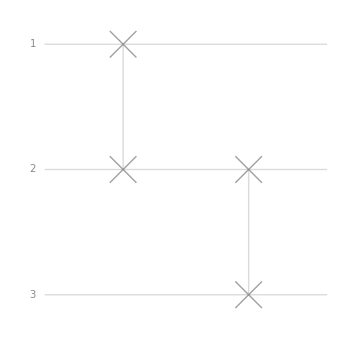

```mathematica
QuantumCircuitOperator[{"SWAP","SWAP"->{2,3}}]["Diagram"]
```

Some arithmetic/operations on operators:

```mathematica
Exp[-ⅈ θ/2 QuantumOperator["X"]]
```

```mathematica
%==QuantumOperator[{"RX",θ}]
```

```mathematica
Sqrt[QuantumOperator["X"]]
```

```mathematica
%==QuantumOperator["SX"]
```

```mathematica
QuantumCircuitOperator[{"X"->{1,2},Sqrt["X"]}]["Diagram"]
```

```mathematica
QuantumOperator["T"+"X"]
```

```mathematica
%==QuantumOperator["T"]+QuantumOperator["X"]
```

```mathematica
QuantumOperator["YY"+"XX"+"ZZ"]
```

```mathematica
QuantumOperator["XX"+"YY"+"ZZ"]==Total[QuantumOperator/@{"XX","YY","ZZ"}]
```

```mathematica
QuantumOperator[{"R",θ,"XX"+"YY"+"ZZ"}]
```

```mathematica
FullSimplify[%==QuantumOperator[{"R",θ,"XX"}]@QuantumOperator[{"R",θ,"YY"}]@QuantumOperator[{"R",θ,"ZZ"}]]
```

One can define controlled operators with many controls and targets:

```mathematica
ctrl1={2};
ctrl0={4,5};
cu=QuantumOperator[{"C",{"X"->{1},"Y"->{3}},ctrl1,ctrl0}]
```

```mathematica
QuantumCircuitOperator[cu]["Diagram"]
```

Ising type of interactions and their Trotter–Suzuki decomposition (fourth order):

```mathematica
op=Table[QuantumOperator["XX",{i,i+1}],{i,5}];
```

```mathematica
qc=QuantumCircuitOperator[{"Trotterization",op,4,1}];
```

```mathematica
qc["Diagram","ShowGateLabels"->False]
```

```mathematica
#["Label"]&/@qc["Operators"]
```

An operator is a tensor flow with input and output:

```mathematica
QuantumOperator["H",{2,3}]["Diagram"]
```

## Named Circuits

```mathematica
QuantumCircuitOperator["Bell"]["Diagram"]
```

```mathematica
QuantumCircuitOperator["Toffoli"]["Diagram"]
```

```mathematica
QuantumCircuitOperator["Fourier"]["Diagram"]
```

```mathematica
QuantumCircuitOperator[{"Fourier",5}]["Diagram"]
```

```mathematica
QuantumCircuitOperator[{"PhaseEstimation",QuantumOperator[{"Phase",2π/5}],3}]["Diagram"]
```

```mathematica
QuantumCircuitOperator[{"BernsteinVazirani","101"}]["Diagram"]
```

```mathematica
QuantumCircuitOperator[{"Graph",RandomGraph[{4,5}]}]["Diagram"]
```

```mathematica
QuantumCircuitOperator[{"Grover",a&&b&&!c||d&&!(a||b)}]["Diagram"]
```

## QuantumBasis

If not specified, we automatically treat everything in the computational basis. Important patterns to remember:

QauntumBasis[{n 1,n 2,...}]

QuantumBasis[n,m]

QuantumBasis[asso]

```mathematica
QuantumBasis[3]
```

```mathematica
QuantumBasis[2,3]
```

```mathematica
QuantumBasis[{3,2,5}]
```

```mathematica
QuantumBasis[<|"up"->{1,1},"down"->{1,-ⅈ}|>]
```

There are also many named basis types:

```mathematica
QuantumBasis["Schwinger"]
```

## QuantumState

The most important pattern to remember is QuantumBasis[arg,qb], with qb defining the basis (if not specified, will be treated automatically as a computational basis, given dimensions of arg.

arg: a list of amplitudes, density matrices or named states:

```mathematica
QuantumState[{1,ⅈ}]
```

```mathematica
QuantumState[{{a,b},{c,d}}]
```

```mathematica
QuantumState[…]
```

```mathematica
QuantumState["RandomMixed"]["DensityMatrix"]//MatrixForm
```

(0.3366+0. ⅈ | 0.211308-0.126269 ⅈ
0.211308+0.126269 ⅈ | 0.6634+0. ⅈ)

```mathematica
QuantumState[{1,ⅈ,3},3]
```

Note padding when qb is not specified:

```mathematica
QuantumState[{1,ⅈ,3}]
```

Named states:

```mathematica
QuantumState["RandomPure",3]
```

```mathematica
state=QuantumState[{"Werner",p,2}]
```

Some arithmetic with states:

```mathematica
x QuantumState[{a,b}]+y QuantumState[{c,d}]
```

Basis transformation: a state defined in the computational basis, then transformed into a Pauli-X basis:

```mathematica
state=QuantumState["RandomPure"];
QuantumState[state,"X"]
```

There are a couple of functions one can apply on quantum states:

QuantumPartialTrace
QuantumDistance
QuantumEntangledQ
QuantumEntanglementMonotone

```mathematica
QuantumPartialTrace[state,{2}]["Formula"]//Simplify
```

For example, Werner states with p>=1/2 are not entangled, while p<1/2 are:

```mathematica
QuantumEntangledQ@QuantumState[{"Werner",1/2,2}]
```

```mathematica
QuantumEntangledQ@QuantumState[{"Werner",1/4,2}]
```

```mathematica
QuantumEntangledQ[QuantumState["GHZ"]]
```

```mathematica
QuantumEntangledQ[QuantumState["GHZ"],{{1},{2}}]
```

The following metrics are supported with the QuantumEntanglementMonotone function: Concurrence (default), EntanglementEntropy, LogNegativity, Negativity, {“RenyiEntropy”, α} and Realignment:

```mathematica
QuantumEntanglementMonotone[QuantumState[{"Werner",1/4,2}]]
```

```mathematica
QuantumEntanglementMonotone[QuantumState[{"Werner",1/4,2}],"LogNegativity"]
```

There are lots of interesting properties one can get from a quantum state, such as StateVector, DensityMatrix, Tensor, Norm, TraceNorm, SchmidtBasis, Conjugate, Transpose (and partial transpose), Purify (and Unpurify), Bend (and Unbend) and Bipartition:

```mathematica
QuantumState["RandomMixed"]["Properties"]
```

Some of these properties return a numerical value (such as entropy) and some return a quantum state (such as transpose or bipartition).

Generate a random pure state of 2-qubits:

```mathematica
r=QuantumState[{"RandomPure",2}]
```

Decompose it (iteration of Schmidt decomposition until getting separable terms; i.e. no entanglement):

```mathematica
r["Decompose"]
```

```mathematica
Map[#["Formula"]&,%,{2}]
```

Similar operator, but final terms are still 2-qubit states (but separable):

```mathematica
#["Formula"]&/@r["Disentangle"]
```

```mathematica
r=QuantumState["RandomMixed",{3}]
```

```mathematica
r["Purify"]
```

Partial tracing over ancillary qudit returns the original state:

```mathematica
QuantumPartialTrace[%,{2}]==r
```

Permute:

```mathematica
QuantumState[{a1,a2,a3,a4}]["Permute",Cycles[{{1,2}}]]
```

An operation can be defined by states (|a><b| format of QM) or an operator (difference in our framework: input/output qudits):

```mathematica
proj=QuantumState["PhiPlus"]["Projector"]
op=QuantumState["PhiPlus"]["Operator"]
```

```mathematica
r=QuantumState[{"RandomPure",2}];
```

```mathematica
proj[r]==QuantumState["PhiPlus"]
```

```mathematica
op[r]==QuantumState["PhiPlus"]
```

Quantum state is a tensor flow with no input and one or more outputs (depending on the number of qudits):

```mathematica
QuantumState["1"]["Diagram"]
```

```mathematica
QuantumState["12"]["Diagram"]
```

## QuantumMeasurementOperator

Either usual PVMs or generic POVMs. Think of it as very similar to a quantum operator (given basis and order):

```mathematica
qm=QuantumMeasurementOperator[{1,3}][QuantumState[{"RandomPure",3}]]
```

```mathematica
qm["ProbabilityPlot"]
```

```mathematica
qm["Probabilities"]
```

```mathematica
qm["StateAssociation"]
```

```mathematica
QuantumMeasurementOperator[{1,2,3}][QuantumState[{"RandomPure",3}]]
```

```mathematica
%["ProbabilityPlot"]
```

POVM:

```mathematica
states={QuantumState[-1/2{1,√3}],QuantumState[-1/2{1,-√3}],QuantumState["0"]};
{e1,e2,e3}=2/3#["Operator"]&/@states;
povm={e1,e2,e3};
```

```mathematica
PositiveSemidefiniteMatrixQ[#["Matrix"]]&/@povm
```

```mathematica
Total[povm]==QuantumOperator["I"]
```

```mathematica
qm=QuantumMeasurementOperator[povm][QuantumState["RandomPure"]]
```

```mathematica
qm["ProbabilityPlot"]
```